```mathematica
Quit[]
```

## Sensible way to devise an accurate expression for log(1+x)

It was easy to devise such a way for ⅇ^x-1.  Now, log(1+x) in the inverse of ⅇ^x-1, because log(1+(ⅇ^x-1))=log(ⅇ^x)=x:

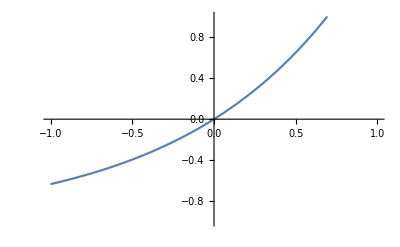

```mathematica
Plot[ⅇ^x-1,{x,-1,1},PlotRange->{-1,1}]
```

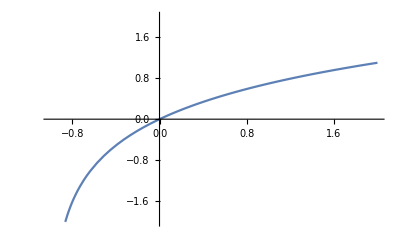

```mathematica
Plot[Log[1+x],{x,-1,2},PlotRange->{-2,2}]
```

Now, we had y=ⅇ^x-1=tanh(x/2)(ⅇ^x+1).  How do we calculate the inverse of it?

y=ⅇ^x-1=tanh(x/2)(ⅇ^x+1)=tan(x/2)(y+2).

x=.1d2 tanh^-1(y/(y+2))

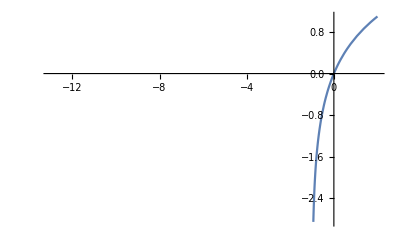

```mathematica
Plot[2ArcTanh[x/(x+2)],{x,-13,2}]
```

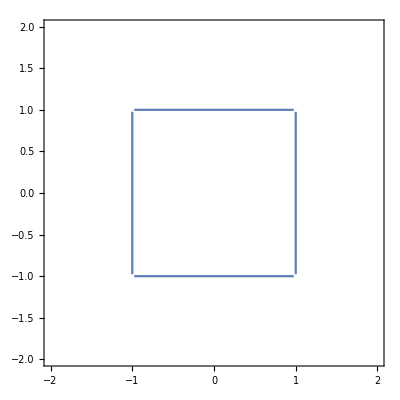

```mathematica
p=∞;ContourPlot[Norm[{x,y},p]==1,{x,-2,2},{y,-2,2}]
```

```mathematica
Manipulate[ContourPlot[Norm[{x,y},p]==1,{x,-1,1},{y,-1,1}],{p,1,4}]
```

```mathematica
p=1;ContourPlot[x^2+y^2==1,{x.1d,-1,1}.1d,{y,-1,1}]
```

ContourPlot::plln: Limiting value -.1d in {(.1d)^2 x,-.1d,.1d} is not a machine-sized real number.

ContourPlot[x^2+y^2==1,{x .1d,-1,1} .1d,{y,-1,1}]

```mathematica
Norm[{1,2}]
```

√5